# Mathematica and Programming Style

## A New Mathematica Programming Style

Kris Carlson

Author, The Way of Mathematica (forthcoming)

|     ▶

## An Historical Perspective on Computer Programming

#### "The computer revolution is a revolution in the way we think and in the way we express what we think. The essence of this change is the emergence of ... procedural epistemology—the study of the structure of knowledge from an imperative point of view, as opposed to the more declarative point of view taken by classical mathematical subjects. Mathematics provides a framework for dealing precisely with notions of 'what is.' Computation provides a framework for dealing precisely with notions of 'how to.'"

Harold Abelson and Gerald Jay Sussman, The Structure and Interpretation of Computer Programs

### Origins of Geometry

Beginnings:	Accurately surveying land boundaries

Destiny: 	Euclid's creation of the first axiomatic science

### Origins of Computer Programming

Beginnings: 	Very abstract notions of computation by Church, Turing, Kleene and others

Destiny: 	The control of complex processes

◀     |     ▶

## The Main Challenges of Modern Science

### Genetic Engineering

Taking control of the analog computer program immanent in DNA-RNA-protein

### Artificial Intelligence

Reverse-engineering the agencies of intelligence created by evolution and creating new ones

Creating and initially controlling intelligences greater than our own

### Nanotechnology

Programming at the atomic and molecular level to control materials

#### These challenges put the Abelson/Sussman thesis in perspective : It' s all about controlling complex processes

### (What about "A Theory of Everything?"

A misnomer. If created, which I doubt it will be, it would be nothing more than a theory of the currently known physical microcosm

Note that computer programming cannot be derived from it—but it can be derived from computer programming)

## Mathematica's Place in History

### Mathematica is a scientific synthesis like those of Euclid, Spinoza, Newton, Locke, Lagrange, Hamilton, Darwin, Maxwell, Gibbs, Shannon, and others

#### "Everything is an expression"—a central unifying syntactic principle like energy in physics or bits in information theory

## More Elements of the Mathematica Synthesis

#### General symbol manipulation program

#### Pattern matching engine

#### A variety of programming styles and devices

#### Axiomatization of lower-level functionality (Table, Map* family, Nest* family, etc.)

#### Interpret and compile modes

#### Interface/IDE—the Front End Notebook

#### Plethora of built-in functions

#### Extension to all special functions via Mathematica Functions site

#### Extensive and growing graphics and visualization capabilities

#### Effectively unlimited notation synthesis

#### Equation solving

#### Numerical analysis/evaluation

#### Axiomatization of higher-level functionality (CellularAutomata, Manipulate, TuringMachine, etc.)

#### gridMathematica

#### Documentation Center

#### MathWorld

#### Presentation and documentation formats

#### webMathematica

#### Demonstrations site

#### Curated data/Data paclets

#### Incipient semantic net (WordData)

## What is the goal of programming style?

### Help manage ever-increasing complexity

### Streamline the human-computer interface from both sides

## A New Mathematica Programming Style

### First principle: Replace all matchfix single argument function applications f[ arg ] with Prefix function applications f @ arg

### Requires some knowledge of the 1000-level Precedence table

### Second principle: Replace nested matchfix with Postfix + pure Function

◀     |     ▶

## Prefix Functional Syntax Cleaner and more efficient than matchfix

### Use prefix function application, @, for single-argument functions

#### Matchfix style:

```mathematica
f[ g[ h[ i [j] ] ] ]
```

#### Prefix style:

```mathematica
f @ g @ h @ i @ j
```

### First two syntactical problems with list- or matchfix-based language

Humans have difficulty parsing deeply nested expressions (>3)

Humans are not regular expression parsers

### Basic Benefits of Prefix style

#### Every pair of brackets we lose makes our expressions easier to read and understand

#### Every pair of brackets for which we don't have to type or move the cursor saves us time

## A Prefix Style Example

#### Each @ tells us there is no complex nesting for that function, no options or arguments to look for, no brackets to match.

#### We can focus our attention on the functions that do use matchfix and identify their arguments and options.

#### There are fewer nested brackets to sort out.

Here's some code from Trott, The Mathematica Guide to Graphics, in matchfix and Prefix styles:

```mathematica
Show[GraphicsArray[
Block[{$DisplayFunction = Identity},
(* display absolute value of 2D Fourier transform *)
 ListDensityPlot[Abs[Fourier[Table[1/#[i, j], {i, 256}, {j, 256}]]], 
                 Mesh -> False, ColorFunction -> (Hue[0.8 #]&)]& /@
                                                       {GCD, LCM}]]]
```

```mathematica
Show@GraphicsArray@
Block[{$DisplayFunction = Identity},
(* display absolute value of 2D Fourier transform *)
 ListDensityPlot[
 Abs@Fourier@Table[1/#[i, j], {i, 256}, {j, 256}], 
                 Mesh -> False, ColorFunction -> (Hue[0.8 #]&)]& /@
                                                       {GCD, LCM}]
```

## More Prefix Style Examples

#### Basic Usages

One argument function definitions:

```mathematica
f[x_] := Sin[x]
```

```mathematica
f@x_ := Sin@x
```

#### One argument functions or assignments:

```mathematica
Log@100^100//N
```

2.11139×10^66

```mathematica
walk1D3@n_:= NestList[#+Random[Real,{-1,1}]&, Random[Real, {-1,1}],n];
```

```mathematica
walk1D3@10
```

{-0.206019,-0.914893,-0.951759,-1.04967,-0.299963,-0.8917,-0.147434,0.764746,1.57289,1.40045,2.13796}

```mathematica
list5 = Range@10;
```

```mathematica
Clear@list5;
```

```mathematica
Histogram@%
```

Histogram[Null]

```mathematica
Needs@"Combinatorica`"
```

#### Multiple one-argument function composition:

```mathematica
f@g@h@i@j@k
```

Sin[g[h[i[j[k]]]]]

```mathematica
First@Rest@Most@Range@10
```

2

#### Function definitions with lists as argument:

```mathematica
f@{a_, b_, c_}:= n@{a,b,c}
```

## But Prefix is an Abbreviated Operator...

...and behaves according to its Precedence. So, for example,

Sin @ n x    doesn't work as intended.

Or, using an example from Wagon, Mathematics in Action, p. 37, this shows the sequence of rightmost nonzero digits of the factorials. The code is correct so far:

```mathematica
f@n_ := Last@DeleteCases[IntegerDigits[n!], 0]
ListPlot@Table[f@n, {n,0,100}]
```

⁃Graphics⁃

Continuing, we naively substitute Prefix for matchfix in IntegerDigits applied to Factorial. What happens?

```mathematica
f@n_ := Last@DeleteCases[IntegerDigits@n!, 0]
ListPlot@Table[f@n, {n,0,100}]
```

⁃Graphics⁃

## Precedence in Mathematica

The main objection to Prefix is that you have to know operator precedence

However this objection applies to all abbreviated operators (+, *, ^, [[ ]], { }, /@, etc.)

Mathematica is endowed with "a variety of special characters that greatly increase readability and elegance"

FORTRAN (FORmula TRANslation; early and primitive, but elegant), Mathematica (an advanced synthesis):
A conscious effort was made to provide a path of least action or smooth transduction from mathematical notation to code

Further, a significant feature of V6 is the addition of >100 undefined operators to facilitate creating user-defined notations

I submit that if you use Prefix, you will use it more often than the most common abbreviated operators

### Precedence directs the order of abbreviated operators' operation

Precedence can be symbolized by parenthetical grouping, such as: a + (b ^ c) versus (a + b) ^ c

The Mathematica reference on precedence in 5.2 was Table A.2.7, now is in tutorial / InputSyntax: Operator Input Forms

It lists all abbreviated operators in tables of decreasing precedence

However, a superior reference can be generated from a little code

## There exists an undocumented function, Precedence

Voila:

```mathematica
Precedence@Prefix
```

640.

It is not listable, but it should be! Either reset Attributes to Listable or just Map it:

```mathematica
Precedence/@ {Prefix, Factorial}
```

{640.,610.}

What happened in the previous slide?
Prefix is a little "stickier" than Factorial==@ sticks to n more than ! does—and so we got (IntegerDigits@n)! instead of IntegerDigits[ n! ]

#### When faced with a few abbreviated operators, map Precedence onto them in the order they present in your expression

```mathematica
a + b * c ^ d - e
```

```mathematica
Precedence /@ {Plus, Times, Power, Minus}
```

{310.,400.,590.,480.}

#### Precedence mnemonics: Think of operator "stickiness" or "binding strength"

## The 1000 - Level Precedence Table

#### Abbreviated Operators

This list includes all nondefined operators as of V5.2 but leaves out over 100 new undefined operators in 6.0

```mathematica
AbbreviatedOperators ={Pi,I, Plus, Infinity,Tilde, Alternatives, Repeated, RepeatedNull, Condition, AddTo, PreIncrement, Increment, Decrement, PreDecrement, Map, MapAll, Apply, Factorial, Factorial2, Prefix, Postfix, Infix,PatternTest,Power,Function,Set, SetDelayed, Rule, RuleDelayed,UpSet,Get,Sum, Product, Coproduct, Cap, Cup, TimesBy,ReplaceAll,Colon,SemiColon,CompoundExpression,Therefore, Because,And, Or, Not,Element, ForAll, Exists, NotExists, Xor, Nand, Nor,SuchThat, Implies, RoundImplies, RightTee, LeftTee, DoubleRightTee, DoubleLeftTee, VerticalSeparator, Union, Intersection, Vee, Wedge, Backslash, Divide, PlusMinus, MinusPlus,CirclePlus, CircleMinus, Times, CircleTimes, CenterDot, Diamond, Star, NonCommutativeMultiply,Cross,Dot, D, Del, Square, SmallCircle, Integrate, Sqrt, StringJoin,  Slot,SlotSequence,Blank,BlankSequence,BlankNullSequence,Optional,Pattern,MessageName,Complex, SubtractFrom, DivideBy,Equal, Greater, Unequal, Less, LessEqual, SameQ, UnsameQ,"=*=", (* only defined operator new in V6? *) Span};
Length@AbbreviatedOperators
```

106

#### $PrecedenceTable, Numerical

```mathematica
$PrecedenceTable={#, Precedence@#}&/@ AbbreviatedOperators//#[[Ordering@#[[All, 2]] ]  ]&//Reverse//Partition[#, Length@#/4//Floor]&//TableForm[#, TableDirections->Row, TableSpacing->{3,1}]&//Style[#, Magnification->.6]&
```

=*= | 1000.
∞ | 1000.
ⅈ | 1000.
MessageName | 750.
Intersection | 750.
SlotSequence | 740.
Slot | 740.
BlankNullSequence | 730.
BlankSequence | 730.
Blank | 730.
Get | 720.
PatternTest | 680.
Sqrt | 670.
SemiColon | 670.
π | 670.
PreDecrement | 660.
Decrement | 660.
Increment | 660.
PreIncrement | 660.
Prefix | 640.
Infix | 630.
Apply | 620.
MapAll | 620.
Map | 620.
Factorial2 | 610.
Factorial | 610. | StringJoin | 600.
Power | 590.
Del | 550.
D | 550.
Square | 540.
SmallCircle | 530.
NonCommutativeMultiply | 510.
Cross | 500.
Dot | 490.
Divide | 470.
Backslash | 460.
Diamond | 450.
Wedge | 440.
Vee | 430.
CircleTimes | 420.
CenterDot | 410.
Times | 400.
Star | 390.
Product | 380.
Coproduct | 360.
Cap | 350.
Cup | 340.
CircleMinus | 330.
CirclePlus | 330.
Integrate | 325.
Sum | 320. | Complex | 310.
MinusPlus | 310.
PlusMinus | 310.
Plus | 310.
Span | 305.
Union | 300.
UnsameQ | 290.
SameQ | 290.
LessEqual | 290.
Less | 290.
Unequal | 290.
Greater | 290.
Equal | 290.
Tilde | 290.
Element | 250.
RoundImplies | 240.
Not | 230.
Nor | 215.
Nand | 215.
Xor | 215.
Or | 215.
And | 215.
Implies | 200.
DoubleLeftTee | 190.
DoubleRightTee | 190.
LeftTee | 190. | RightTee | 190.
SuchThat | 180.
RepeatedNull | 170.
Repeated | 170.
Alternatives | 160.
Pattern | 150.
Optional | 140.
Condition | 130.
RuleDelayed | 120.
Rule | 120.
ReplaceAll | 110.
DivideBy | 100.
SubtractFrom | 100.
TimesBy | 100.
AddTo | 100.
Function | 90.
Colon | 80.
Postfix | 70.
VerticalSeparator | 60.
Because | 50.
Therefore | 50.
UpSet | 40.
SetDelayed | 40.
Set | 40.
CompoundExpression | 10.
NotExists | 0.

◀     |     ▶

#### $PrecedenceTable, Alphabetical

```mathematica
{#, Precedence@#}&/@ AbbreviatedOperators//#[[Ordering@#[[All, 1]] ]  ]&//Partition[#, Length@#/4//Floor]&//TableForm[#, TableDirections-> Row, TableSpacing-> {3,1}]&//Style[#, Magnification->.6]&
```

ⅈ | 1000.
=*= | 1000.
AddTo | 100.
Alternatives | 160.
And | 215.
Apply | 620.
Backslash | 460.
Because | 50.
Blank | 730.
BlankNullSequence | 730.
BlankSequence | 730.
Cap | 350.
CenterDot | 410.
CircleMinus | 330.
CirclePlus | 330.
CircleTimes | 420.
Colon | 80.
Complex | 310.
CompoundExpression | 10.
Condition | 130.
Coproduct | 360.
Cross | 500.
Cup | 340.
D | 550.
Decrement | 660.
Del | 550. | Diamond | 450.
Divide | 470.
DivideBy | 100.
Dot | 490.
DoubleLeftTee | 190.
DoubleRightTee | 190.
Element | 250.
Equal | 290.
Exists | 0.
Factorial | 610.
Factorial2 | 610.
ForAll | 0.
Function | 90.
Get | 720.
Greater | 290.
Implies | 200.
Increment | 660.
Infix | 630.
Integrate | 325.
Intersection | 750.
LeftTee | 190.
Less | 290.
LessEqual | 290.
Map | 620.
MapAll | 620.
MessageName | 750. | MinusPlus | 310.
Nand | 215.
NonCommutativeMultiply | 510.
Nor | 215.
Not | 230.
NotExists | 0.
Optional | 140.
Or | 215.
Pattern | 150.
PatternTest | 680.
π | 670.
Plus | 310.
PlusMinus | 310.
Postfix | 70.
Power | 590.
PreDecrement | 660.
Prefix | 640.
PreIncrement | 660.
Product | 380.
Repeated | 170.
RepeatedNull | 170.
ReplaceAll | 110.
RightTee | 190.
RoundImplies | 240.
Rule | 120.
RuleDelayed | 120. | SameQ | 290.
SemiColon | 670.
Set | 40.
SetDelayed | 40.
Slot | 740.
SlotSequence | 740.
SmallCircle | 530.
Span | 305.
Sqrt | 670.
Square | 540.
Star | 390.
StringJoin | 600.
SubtractFrom | 100.
SuchThat | 180.
Sum | 320.
Therefore | 50.
Tilde | 290.
Times | 400.
TimesBy | 100.
Unequal | 290.
Union | 300.
UnsameQ | 290.
UpSet | 40.
Vee | 430.
VerticalSeparator | 60.
Wedge | 440.

◀     |     ▶

#### Suggestions for WRI

Use the Precedence table in documentation instead of Operator Input Forms table

Add Tooltips with Precedence to all abbreviated operators so we can cursor them and see their Precedence

Map Tones on to all abbreviated operators' Tooltips, scaled appropriately, so we can cursor them and hear their Precedence

(And liberate Tones from CellularAutomata; Tones should permeate Mathematica—Mathematica should sound like R2D2)

#### Questions for WRI

How does PrecedenceForm work?

How do the "structural elements," all having Precedence = 670, work?

Why not make Comma right-associative with actual Precedence 670 so we can write multiple-argument Prefix functions like this:

```mathematica
f@a,b,c := g@i,j,k
```

## Next: Syntax Problems 3, 4, 5 and 6

#### Nested matchfix violates various programming good practices

"The guiding principle [of the order of statements of code] is the Principle of Proximity: Keep related actions together."

"If you draw a box around each statement, they should not overlap."

"As a general principle, make the program read from top to bottom rather than jumping around. Experts agree that top-to-bottom order contributes most to readability."

"The Fundamental Theorem of Formatting is that good visual layout shows the logical structure of the program."
									—Steve McConnell, Code Complete

'The price paid for functional style programs without excess auxiliary variables is "a large number of brackets."'
									—Michael Trott

#### Postfix "afterthought" functions can't take arguments, which stymies extended command-line programming

```mathematica
3 Cos[x] + 2 Cos[2 x] + Cos[3 x]//Plot[  ??
```

#### Initiates to functional programming need to learn to think "inside out" or right-to-left

#### Procedural programmers can be less than thrilled with functional syntax

#### We would like to write code to emphasize what's important, downplay what's not

## Illustration of Matchfix Readability Problems

### Compare three versions of a simple function using increasing numbers of optional arguments

### Note the violation of the Principle of Proximity

### Do boxes drawn around statements overlap?

#### In example #3, note the code is structured to emphasize whichever expression we wish, in this case, GraphicsRow, not Manipulate, which is just the "wrapper"

```mathematica
Manipulate[GraphicsRow[{Graphics[Disk[]],Graphics[Disk[]],Graphics[Disk[]]},Spacings->Scaled[i], Frame->True, Dividers-> All],  {i, .1, 1}]
```

```mathematica
Manipulate[GraphicsRow[{Graphics[Disk[]],Graphics[Disk[]],Graphics[Disk[]]},Spacings->Scaled[i], Frame->True, Dividers-> All, Alignment->{Center,Center} ,AlignmentPoint->Center,AspectRatio->Automatic,Axes->False,AxesLabel->None,AxesOrigin->Automatic,AxesStyle->{}, Background->None,BaselinePosition->Automatic,BaseStyle->{}, ColorOutput->Automatic,ContentSelectable->Automatic,DisplayFunction:>$DisplayFunction,Dividers->None,Epilog->{}],  {i, .1, 1}]
```

```mathematica
GraphicsRow[{Graphics@Disk[],Graphics@Disk[],Graphics@Disk[]},Spacings->Scaled@i, Frame->True, Dividers-> All, Alignment->{Center,Center} ,AlignmentPoint->Center,AspectRatio->Automatic,Axes->False,AxesLabel->None,AxesOrigin->Automatic,AxesStyle->{}, Background->None,BaselinePosition->Automatic,BaseStyle->{}, ColorOutput->Automatic,ContentSelectable->Automatic,DisplayFunction:>$DisplayFunction,Dividers->None,Epilog->{}]
//Manipulate[#,  {i, .1, 1}]&
```

### And the more nested the function, the worse it is

◀     |     ▶

## Postfix/Pure Function Style: Functional-Procedural Fusion

### A Solution: extended usage of Postfix and pure Function

As an alternative to this 'traditional' usage of matchfix:

```mathematica
expr7 [ expr6 [ expr5 [expr4 [expr3 [expr2 [expr1 ] ] ] ] ] ] ]
```

Consider writing this, using Postfix and pure Function:

```mathematica
expr1 // expr2 # & // expr3 # & // expr4 # & // expr5 # & // expr6 # & // expr7 # &
```

And you can write it down the page, too:

```mathematica
expr1 //
expr2 # & //
expr3 # & //
expr4 # & //
expr5 # & //
expr6 # & //
expr7 # &
```

It works as simply as this:

```mathematica
expr1 // expr2#& => expr2[expr1]
```

### Amounts to a fusion of procedural and functional styles

#### Functional programming that looks procedural

## FP Fusion Examples

#### Command line or one-liner

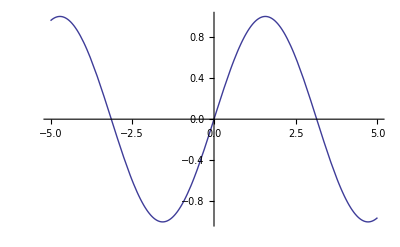

```mathematica
Sin@x//Plot[#,{x, -5, 5}]&
```

#### Extended one-liner or function

This fits the general pattern of a class of functions. You generate some data or intialize a function, then perform a few transformations on it, and then you want to view it. 

Here we write it as a readable one-liner, sequentially across the page.

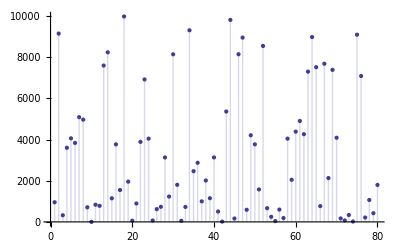

```mathematica
Clear@g;
g@x_ := RandomReal[]; 
Table[g@i, {i, 100}] //Take[#, 80]& //100 #& //#^2& //ListPlot[#, Filling->Axis]&
```

Or sequentially down the page, nice and clean.

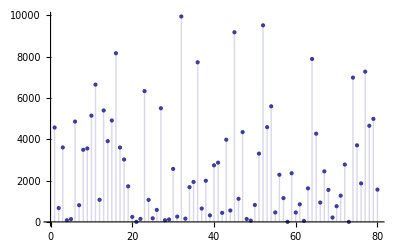

```mathematica
g@x_ := RandomReal[]; 
Table[g@i, {i, 100}] //
Take[#, 80]& //
100 #& //
#^2& //
ListPlot[#, Filling->Axis]&
```

## Summary

### Computer programming's destiny is to control high-order complexity

### Mathematica is a modern scientific synthesis whose core is the most advanced programming language paradigm

### Mathematica's destiny is to play a lead role in the scientific challenges of our age

#### V6 shows its capabilities go far beyond those of any other programming language

### Prefix and FP Fusion are a suggested improvement in syntax toward more understandable programs

Comments and suggestions are welcome: carlsonkw@gmail.com

## Acknowledgements and References

#### Stephen Wolfram

The Mathematica Book
Code examples in A New Kind of Science

#### Roman Maeder, harry calkins

A First Course in Mathematica
Programming in Mathematica

#### Roman Maeder

Programming in Mathematica 2nd Ed.
The Mathematica Programmer
The Mathematica Programmer II
Computer Science with Mathematica

#### David B. Wagner

Power Programming in Mathematica: The Kernel

#### John W. Gray

Mastering Mathematica, 2nd Ed.: Programming Methods and Applications

#### Michael Trott

The Mathematica Guidebook: Programming

#### Paul R. Wellin, Richard J. Gaylord, and Samuel N. Kamin

An Introduction to Programming with Mathematica, 3rd Ed.

#### Christian Jacob

Illustrating Evolutionary Computation with Mathematica

#### Nancy Blachman

Mathematica: A Practical Approach

#### Stan Wagon

Mathematica in Action

#### And thanks to the attendees of this talk who had valuable suggestions, in particular Paul Abbott, and their forbearance of my first effort using a Mathematica slide show